torque of the NS.
There are two ways to calculate the torque of the neutron stars:
1. N=(M^(_.))_in*R_0^2*Ω_K(R_0)=(M^(_.))_in*(G*M*R_0)^(1/2)
2. N=I*Ω̇=-2π*I*Ṗ/P^2
where (M^(_.))_in is the mass transfer rate in the inner radius of the accretion disk, sometime is also the accretoin rate; R_0=ξ*R_A is the the inner radius of the accretion disk, and where R_A=(μ^4/(2*G*M*(Ṁ)_acc^2))^(1/7) is the Alfven radius.

```mathematica
Clear["`*"]

(*constant*)
G=6.67*10^-8;
Msun=2.*10^33;
c=3.*10^10;
R=10^6;(*radius of the NS*)
MdotEdd=1.946*10^18;(*Eddington accretion rate*)
Mdotcr=1.9*10^22;(*3*10^-4 Msun yr^-1*)
mdotcr=Mdotcr/MdotEdd;
M=2.8*10^33;
Irot=10^45;(*moment of inertia*)
xi=0.5;

P=31.6;
Pdot=-5.56*10^-7;

mu=0.5*B*R^3;

Mdotacc=Mdotin;
R0=xi*(mu^4/(2*G*M*Mdotacc^2))^(1/7);

torque1=Mdotin*(G*M*R0)^(1/2);
torque2=-2*Pi*Irot*Pdot/P^2;
```

```mathematica
NSolve[torque1==torque2,Mdotin]
```

{{Mdotin→-(6.30834×10^23)/B^(1/3)},{Mdotin→-(0.+6.30834×10^23 ⅈ)/B^(1/3)},{Mdotin→(0.+6.30834×10^23 ⅈ)/B^(1/3)},{Mdotin→(6.30834×10^23)/B^(1/3)}}

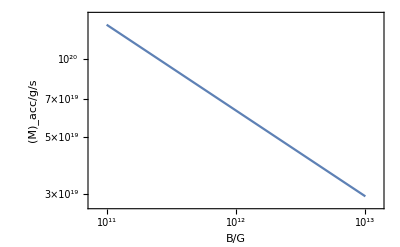

```mathematica
Mdotin=(6.30834*^23)/B^(1/3);
LogLogPlot[Mdotin,{B,10^11,10^13},Frame->True,FrameLabel->{"B/G","(Ṁ)_acc/g/s"}]
```

```mathematica
Mdotin/.B->10^12
```

6.30834×10^19